## 附录：计算晶胞参数

```mathematica
(*定义四舍五入后的偏差函数*)
```

```mathematica
f[x_]:=Abs[x-Round[x]]
```

```mathematica
(*输入所有测量得到的晶面间距*)
```

```mathematica
d={3.1352,1.9199,1.6373,1.5676,1.3576,1.2458,1.1085}
```

```mathematica
(*显然a不能小于测得的d中的最大值，也不能超出10^(-10)m的数量级*)
(*现在要找到a使得所有a/d的平方都近似为一个整数，绘制误差函数定性分析*)
```

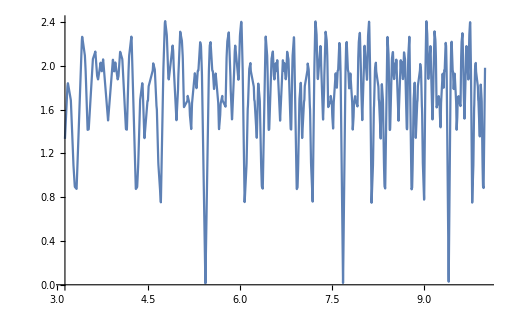

```mathematica
Plot[Sum[f[(a/d[[i]])^2],{i,1,7}],{a,3.1352,10.0000}]
```

```mathematica
(*从图像中可看出要找的a在5~6之间，生成一个庞大的矩阵*)
```

```mathematica
T=Table[Sum[f[(a/d[[i]])^2],{i,1,7}],{a,5,6,0.00001}];
```

```mathematica
(*寻找最小值出现的位置*)
```

```mathematica
Position[T,Min[T]]
```

{{43034}}

```mathematica
a=5+0.00001*43034
```

5.43034

```mathematica
(*计算a/d比值*)
```

```mathematica
(5.43034/3.1352)^2
```

3.00002

```mathematica
(*由此得知测得数据中晶面指数最小的是111面，从而对晶胞参数a可以修正为*)
```

```mathematica
a=Sqrt[1^2+1^2+1^2]*3.1352
```

5.43033

```mathematica
(*与软件拟合给出的5.43029相对误差仅为7E-4*)
```